```mathematica
ClearAll;

Off[NonlinearModelFit::cvmit,NIntegrate::ncvb,FindFit::cvmit,NonlinearModelFit::sszero]
```

Definition of Gauß, Lorentz, and Lorentz-transformed Lorentz functions

ILUM = (∫^∞)_e_th de 1/((σ_r-e)^2+σ_i^2)·1/((a_n-e)^2+b_n^2)

```mathematica
hat[l_]:=Sqrt[2 l+1];

j0=0.5;jlit=0.5;
MUL=1;
pi="-";

v18uixpath="/home/kirscher/kette_repo/ComptonLIT/v18uix_helium3/";

ILana[sr_,si_,a_,b_,eth_,c_]:=c^2/(((sr-a)^2+(si-b)^2) ((sr-a)^2+(si+b)^2)) (((sr-a)^2+b^2-si^2)/si (Pi/2+ArcTan[(sr-eth)/si])+((sr-a)^2-b^2+si^2)/b (Pi/2+ArcTan[(a-eth)/b])+(sr-a) Log[((sr-eth)^2+si^2)/((a-eth)^2+b^2)]);
Lorentz[e_,a_,b_,c_]:=c^1/((a-e)^2+b^2);
```

import LIT data

i)    import data
       calculated with  <cpts_helion_v18uix_GAUSS_RGM.nb>

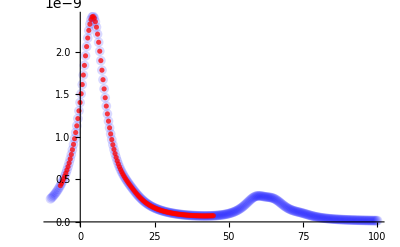

```mathematica
dataCrossLitfull=N[ToExpression[Import[v18uixpath<>"real_LIT_J_"<>ToString[jlit],"Table","FieldSeparators"->" ; "]]];
dataCrossLit=N[ToExpression[Import[v18uixpath<>"real_LIT_J_"<>ToString[jlit],"Table","FieldSeparators"->" ; "]]][[10;;150]];

nbrS=Length[dataCrossLit];
ub=dataCrossLit[[-1]][[1]];
lb=dataCrossLit[[1]][[1]];
sStellen=Range[lb,ub,(ub-lb)/nbrS];

emin=0.0;emax=100;
file=v18uixpath<>"E0.dat";

e0=Read[file];Close[file];
eth=0.0;
si=5;

Show[
ListPlot[dataCrossLitfull,PlotStyle->{Blue,Opacity[0.15],Large},PlotRange->Full,PlotMarkers->{Automatic, Medium}],
ListPlot[dataCrossLit,PlotStyle->{Red,Opacity[0.75]},AxesLabel->{"σ_r [MeV]","L(σ) [mb·MeV^-1]"}]
]
```

Determine appropriate (inspired) Lorentz parameters by fitting to the chosen set of cross-section data

f_n(e)=(θ(e-e_th))/((a_n-e)^2+b_n^2)

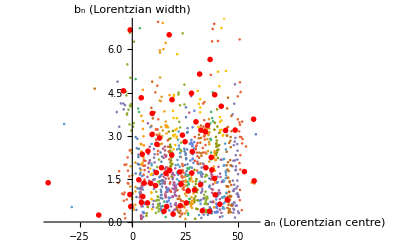

```mathematica
dataCross=Import["/home/kirscher/kette_repo/ComptonLIT/triton_inclusive_photo_abs.csv"];
dataCross=dataCrossLit;

inspireddim=180;

thup={60,14,10};
thlo={-1.9,0.1,10^-12};

tmpdim=0;
inspiredbas={};
While[tmpdim≤inspireddim,{

bassdim=8;

modelLorentzABC=Sum[ILana[srLn,si,aLn@i,bLn@i,eth,cLn@i],{i,bassdim}];

nlmLABC=NonlinearModelFit[dataCross,modelLorentzABC,Flatten[Table[{{aLn@i,RandomReal[{-4.1,52.14}]},{bLn@i,RandomReal[{.3,3.5}]},{cLn@i,RandomReal[{0.0,100.2}]}},{i,bassdim}],1],srLn];

basispara=Select[Table[{aLn@i,bLn@i,cLn@i},{i,bassdim}]/.nlmLABC["BestFitParameters"],Abs[#[[1]]]>thlo[[1]]&&Abs[#[[1]]]<thup[[1]]&&#[[2]]>thlo[[2]]&&Abs[#[[2]]]<thup[[2]]&&Abs[#[[3]]]>thlo[[3]]&&Abs[#[[3]]]<thup[[3]]&][[All,1;;2]];
If[Length[basispara]>0,AppendTo[inspiredbas,basispara](*Print[nlmLABC["AdjustedRSquared"]];*)];
tmpdim=Length[inspiredbas];
}]
inspiredbas=Sort[Flatten[inspiredbas,1],#1[[1]]>#2[[1]]&];

inspireddimclustered=70;
tmp=FindClusters[inspiredbas,inspireddimclustered,Method->"KMedoids",DistanceFunction->EuclideanDistance];
lorentzbas=Map[RandomChoice][tmp];
Show[ListPlot[tmp,AxesLabel->{"a_n (Lorentzian centre)","b_n (Lorentzian width)"},PlotMarkers->{None,Small}],
ListPlot[lorentzbas,PlotMarkers->{"♛",8},PlotStyle->Red]]
```

Adapt the inspired (see above) and a randomly chosen Lorentz-transformed Lorentz basis to the model LIT and compare the thereby reconstructed cross section with the original data

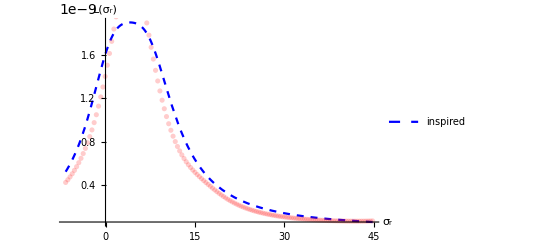

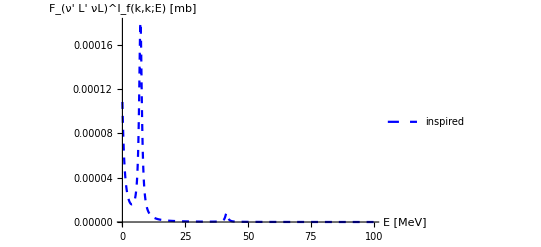

```mathematica
Clear[a];
desiredclusteranzahl=16;
lorentzbasinspcl=FindClusters[Tuples[{lorentzbas[[All,1]],lorentzbas[[All,2]]}],desiredclusteranzahl,DistanceFunction->EuclideanDistance, RandomSeeding->1234][[All,1]];
(*BrayCurtisDistance,ChebyshevDistance,EuclideanDistance*)
lorentzbasinsprnd=DeleteDuplicates[RandomChoice[lorentzbas,desiredclusteranzahl]];

lorentzbasinsp=lorentzbasinsprnd;
inspdim=Length[lorentzbasinsp];
coeffs=Array[a,inspdim];

(*constraint=Table[1./((lorentzbasinsp[[n]][[1]]-eth)^2+lorentzbasinsp[[n]][[2]]^2),{n,inspdim}];
Values[nlmL].constraint;*)

LinearLorentzModel=Sum[ILana[sigmaR,si,lorentzbasinsp[[i]][[1]],lorentzbasinsp[[i]][[2]],eth,coeffs[[i]]],{i,inspdim}];
nlmL=FindFit[dataCrossLit,LinearLorentzModel,coeffs,sigmaR];
(*nlmL=FindFit[dataCrossLit,{LinearLorentzModel,Table[coeffs[[n]]>0,{n,1,inspdim}]},coeffs,sigmaR]*)

expan[x_]:=LinearLorentzModel/.nlmL/.sigmaR->x;

modelResponse[e_]:=HeavisideTheta[e-eth] Sum[Lorentz[e,lorentzbasinsp[[n]][[1]],lorentzbasinsp[[n]][[2]],coeffs[[n]]],{n,inspdim}]/.nlmL;

Show[
Plot[expan[x],{x,lb,ub},PlotLegends->{"inspired"},PlotRange->Full,AxesLabel->{"σ_r","L(σ_r)"},PlotStyle->{Blue,Dashed}],
ListPlot[dataCrossLit,PlotStyle->{Red,Opacity[0.2]},PlotLegends->"Gaussian LIT data"]
]

Show[
Plot[modelResponse[e],{e,emin,emax},PlotRange->Full,PlotLegends->{"inspired"},AxesLabel->{"E [MeV]","F_(ν' L' νL)^I_f(k,k;E) [mb]"},PlotStyle->{Blue,Dashed}]
]
```

strength functions from partial strength functions

F_((ν'L'νL)J)^(I_f I_i;J')(k,k;E)=(E-E_0)^2/(4π)∑_J' {L
I_fL'
I_iJ
J'} F_ν'L'νL^(I_f I_i;J')(k,k;E)
the energy-dependent prefactor is Siegert-form specific and does not appear in general!

```mathematica
Ll=1;
Llp=1;
Ji=Jf=0.5;
Jj=0;
Jjp=1/2;
strengthfunction[ee_]:=(4 Pi)^(-1) (ee-e0)^2 SixJSymbol[{Ll,Llp,Jj},{Jf,Ji,Jjp}] modelResponse[ee];
```

real and imaginary parts of the (generalized) polarizabilities from strength functions

Im{P_(if,J)^res(M^ν' L',M^ν L,k',k)}=2 π^2 (-)^(L+I_f+I_i)L̂ L̂' [F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i+k)+(-)^(L+L'+J)F_((ν'L'νL)J)^(I_f I_i)(k,k;E_i-k')]
The second term does not contribute because the initial state is the ground- and not an excited state!
Specifically:          Im{P_(if,J)^res(E1,E1,k,k)}=6 π^2  F_((11)0)^(1/2 1/2)(k,k;-B(3He)+k)

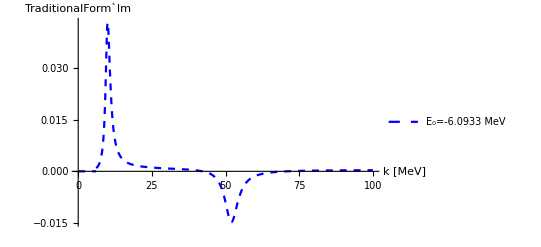

```mathematica
ImPEoneJ[k_]:=2 Pi^2 (-1)^(Ll+Jf+Ji) hat[Ll] hat[Llp] strengthfunction[e0+k]
Plot[ImPEoneJ[k],{k,emin,emax},PlotRange->Full,PlotLegends->{"E_0="<>ToString[e0]<>" MeV"},AxesLabel->{"k [MeV]","TraditionalForm`Im"},PlotStyle->{Blue,Dashed}]
```

Re{P_(if,J)^res(M^ν' L',M^ν L,k',k)}=2π (-)^(L+I_f+I_i)L̂ L̂'  𝓅∫_E_0^∞ dE[(F_((ν'L'νL)J)^(I_f I_i)(k,k;E))/(E-E_i-k)+(-)^(L+L'+J)(F_((ν'L'νL)J)^(I_f I_i)(k,k;E))/(E-E_i+k')]

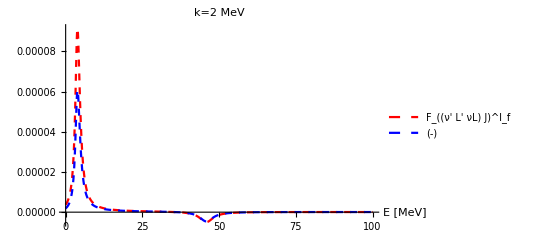

```mathematica
prefak=2 Pi (-1)^(Ll+Jf+Ji) hat[Ll] hat[Llp];
RePEoneJkernelA[e_,k_]:= strengthfunction[e]/(e-(e0+k));
RePEoneJkernelB[e_,k_]:=(-1)^(Ll+Llp+Jj) strengthfunction[e]/(e-(e0-k));
kk=2;
Plot[{RePEoneJkernelA[ee,kk],RePEoneJkernelB[ee,kk]},{ee,emin,emax},PlotRange->Full,PlotLegends->{"F_((ν' L' νL) J)^I_f","(-)"},AxesLabel->{"E [MeV]",""},PlotStyle->{{Red,Dashed},{Blue,Dashed}},PlotLabel->"k="<>ToString[kk]<>" MeV"]
```

```mathematica
gPA[kk_]:=NIntegrate[RePEoneJkernelA[ee,kk],{ee,e0,e0+kk,Infinity},Method->"PrincipalValue"]
gPB[kk_]:=NIntegrate[RePEoneJkernelB[ee,kk],{ee,e0,e0-kk,Infinity},Method->"PrincipalValue"]
genPol[kk_]:=NIntegrate[RePEoneJkernelA[ee,kk],{ee,e0,e0+kk,Infinity},Method->"PrincipalValue"]+NIntegrate[RePEoneJkernelB[ee,kk],{ee,e0,e0-kk,Infinity},Method->"PrincipalValue"]
```

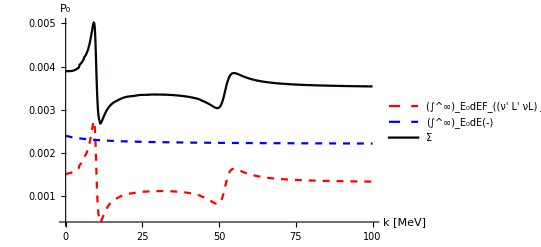

```mathematica
kmax=100;
Plot[{gPA[kk],gPB[kk],genPol[kk]},{kk,0.001,kmax},PlotRange->Full,PlotLegends->{"(∫^∞)_E_0dEF_((ν' L' νL) J)^I_f","(∫^∞)_E_0dE(-)","Σ"},AxesLabel->{"k [MeV]","P_0"},PlotStyle->{{Red,Dashed},{Blue,Dashed},{Black}},PlotPoints->10]
```